## Properties of ZrC

#### All the properties available;

```mathematica
ElementData["Properties"]
```

{Abbreviation,AdiabaticIndex,AllotropeNames,AllotropicMultiplicities,AlternateNames,AlternateStandardNames,AtomicMass,AtomicNumber,AtomicRadius,Block,BoilingPoint,BrinellHardness,BulkModulus,CASNumber,Color,CommonCompoundNames,CovalentRadius,CriticalPressure,CriticalTemperature,CrustAbundance,CrystalStructure,CuriePoint,DecayMode,Density,DiscoveryCountries,DiscoveryYear,ElectricalConductivity,ElectricalType,ElectronAffinity,ElectronConfiguration,ElectronConfigurationString,Electronegativity,ElectronShellConfiguration,FusionHeat,GasAtomicMultiplicities,Group,HalfLife,HumanAbundance,IconColor,IonizationEnergies,IsotopeAbundances,KnownIsotopes,LatticeAngles,LatticeConstants,Lifetime,LiquidDensity,MagneticType,MassMagneticSusceptibility,MeltingPoint,Memberships,MeteoriteAbundance,MohsHardness,MolarMagneticSusceptibility,MolarVolume,Name,NeelPoint,NeutronCrossSection,NeutronMassAbsorption,OceanAbundance,Period,Phase,PoissonRatio,QuantumNumbers,Radioactive,RefractiveIndex,Resistivity,Series,ShearModulus,SolarAbundance,SoundSpeed,SpaceGroupName,SpaceGroupNumber,SpecificHeat,StableIsotopes,StandardName,SuperconductingPoint,ThermalConductivity,ThermalExpansion,UniverseAbundance,Valence,VanDerWaalsRadius,VaporizationHeat,VickersHardness,VolumeMagneticSusceptibility,YoungModulus}

#### Make a plot of the density for the first 100 or so elements;

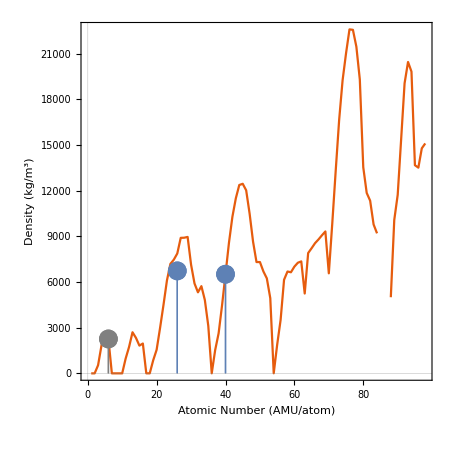

```mathematica
Show[{ListLinePlot[Table[ElementData[z,"Density"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,Black],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,Black],Style["Density (kg/m^3)",20,Black]},ImageSize->450,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"Density"]},{z,6,6}],PlotStyle->Directive[Gray,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"Density"]},{z,40,40}],PlotStyle->Directive[PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(12+40)/2,6.73*10^3}},PlotStyle->Directive[PointSize[0.03]],Filling->Bottom,FillingStyle->Thick]}]
```